# Infinite 3D medium, Isotropic Point Source, Linearly-Anisotropic Scattering

## Gamma-2 Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine
b - anisotropy parameter

### Namespace

```mathematica
Begin["inf3DisopointlinanisoscatterGamma2`"]
```

inf3DisopointlinanisoscatterGamma2`

## Analytical results

```mathematica
LegPcoeff[k_,j_]:=DifferenceRoot[Function[{y,n},{(-n+k) (1+n+k) y[n]+(1+n) (2+n) y[2+n]==0,y[0]==LegendreP[k,0],y[1]==-(1+k) LegendreP[1+k,0]}]][j]
```

```mathematica
Fpc[k_,m_,pc_]:=Module[{integrand},
integrand=I^m Sum[LegPcoeff[m,i](1/I)^i D[SphericalBesselJ[k,x ],{x,i}],{i,0,m}]/.x->u z;
Integrate[pc[z]integrand,{z,0,Infinity},Assumptions->u>0]
]
```

### Collision rate density

collision rate density Cc[r] due to correlated emission:

#### derivation

```mathematica
Clear[A,b,c,r,h];
```

```mathematica
cpc[s_]:=c Exp[-s]s
```

```mathematica
f00=Fpc[0,0,cpc];
f01=Fpc[0,1,cpc];
f11=Fpc[1,1,cpc];
o=2;

A[0]:=1;A[1]:=b;
hsystem=Table[h[k]==2/Pi u F[k,0]+ Sum[A[m]h[m]F[k,m],{m,0,o-1}],{k,0,o-1}];
hsystemsolve=Simplify[Solve[hsystem,Table[h[i],{i,0,o-1}]]/.F[0,0]->f00/.F[0,1]->f01/.F[1,1]->f11/.F[1,0]->-f01]
```

{{h[0]→(2 c u (b c u^2+u^4-b c (1+u^2) ArcTan[u]^2))/(π (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2)),h[1]→(2 c u^3 (-u+(1+u^2) ArcTan[u]))/(π (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))}}

```mathematica
Clear[r];CF0=(2k+1)1/(4 Pi  c)(h[k])u SphericalBesselJ[k,r u]/.k->0/.hsystemsolve//FullSimplify//First
```

(u (b c u^2+u^4-b c (1+u^2) ArcTan[u]^2) Sin[r u])/(2 π^2 r (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u])))

```mathematica
CF0plus=(2k+1)1/(4 Pi  c)(h[k]-(2u)/Pi f00)u SphericalBesselJ[k,r u]/.k->0/.hsystemsolve//FullSimplify//First
```

(u^2 (-1/(1+u^2)+(b c u^2+u^4-b c (1+u^2) ArcTan[u]^2)/(-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u]))) Sinc[r u])/(2 π^2)

#### result

```mathematica
Ccexact[r_,t_,c_,b_]:=NIntegrate[(u (b c u^2+u^4-b c (1+u^2) ArcTan[u]^2) Sin[r u])/(2 π^2 r (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u]))),{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
Ccexact2[r_,t_,c_,b_]:=(Exp[-r]r)/(4 Pi r^2) +NIntegrate[(u^2 (-1/(1+u^2)+(b c u^2+u^4-b c (1+u^2) ArcTan[u]^2)/(-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u]))) Sinc[r u])/(2 π^2),{u,0,Infinity},Method->"LevinRule"]
```

### uncorrelated emission

```mathematica
pu[s_]:=c 1/2 Exp[-s](1+s)
```

```mathematica
f00u=Fpc[0,0,pu];
f01u=Fpc[0,1,pu];
f11u=Fpc[1,1,pu];
```

```mathematica
o=2;
Clear[A,b,c,r,h];
A[0]:=1;A[1]:=b;
hsystem=Table[h[k]==2/Pi u Fu[k,0]+ Sum[A[m]h[m]F[k,m],{m,0,o-1}],{k,0,o-1}];
hsystemsolve=Simplify[Solve[hsystem,Table[h[i],{i,0,o-1}]]/.A[1]->b/.F[0,0]->f00/.F[0,1]->f01/.F[1,1]->f11/.F[1,0]->-f01/.Fu[1,0]->-Fu[0,1]/.Fu[0,1]->f01u/.Fu[0,0]->f00u]
```

{{h[0]→(c u (2 b c u^2+u^4+(u^3+u^5) ArcTan[u]-2 b c (1+u^2) ArcTan[u]^2))/(π (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2)),h[1]→(c u^2 (-c u^2+u^4+c (1+u^2) ArcTan[u]^2))/(π (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))}}

```mathematica
Clear[r];CF0=(2k+1)1/(4 Pi  c)(h[k])u SphericalBesselJ[k,r u]/.k->0/.hsystemsolve//FullSimplify
```

{(u (2 b c u^2+u^4+(1+u^2) ArcTan[u] (u^3-2 b c ArcTan[u])) Sin[r u])/(4 π^2 r (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u])))}

```mathematica
Cuexact[r_,t_,c_,b_]:=NIntegrate[(u (2 b c u^2+u^4+(1+u^2) ArcTan[u] (u^3-2 b c ArcTan[u])) Sin[r u])/(4 π^2 r (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u]))),{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
Clear[r];CF0=(2k+1)1/(4 Pi  c)(h[0]-(2 u)/Pi f00u)u SphericalBesselJ[k,r u]/.k->0/.hsystemsolve//FullSimplify
```

{(c (u^5+b u^3 (c+u^2)-(1+u^2) ArcTan[u] (-b c u^2+(-1+b) u^4+b c ArcTan[u] (u+(1+u^2) ArcTan[u]))) Sin[r u])/(4 π^2 r (1+u^2) (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u])))}

```mathematica
Cuexact2[r_,t_,c_,b_]:=(1/2 Exp[-r](1+r))/(4 Pi   r^2)+NIntegrate[(c (u^5+b u^3 (c+u^2)-(1+u^2) ArcTan[u] (-b c u^2+(-1+b) u^4+b c ArcTan[u] (u+(1+u^2) ArcTan[u]))) Sin[r u])/(4 π^2 r (1+u^2) (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u]))),{u,0,Infinity},Method->"LevinRule"]
```

### scalar flux / fluence

```mathematica
cXc[s_]:= c ⅇ^-s (1+s)
```

```mathematica
fX00= Fpc[0,0,cXc];
fX01= Fpc[0,1,cXc];
```

```mathematica
fluxh0=Sum[h[m]A[m]FX[0,m],{m,0,o-1}]/.hsystemsolve/.FX[0,0]->fX00/.FX[0,1]->fX01//Simplify//First
```

-(2 c^2 (-u^3 (u^2+b (c+u^2))-u^2 (1+u^2) (u^2+b (c-u^2)) ArcTan[u]+b c u (1+u^2) ArcTan[u]^2+b c (1+u^2)^2 ArcTan[u]^3))/(π (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))

```mathematica
Clear[r];CF0=(2k+1)1/(4 Pi c)(fluxh0)u SphericalBesselJ[k,r u]/.k->0
```

-((c u (-u^3 (u^2+b (c+u^2))-u^2 (1+u^2) (u^2+b (c-u^2)) ArcTan[u]+b c u (1+u^2) ArcTan[u]^2+b c (1+u^2)^2 ArcTan[u]^3) SphericalBesselJ[0,r u])/(2 π^2 (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2)))

```mathematica
ϕcexact[r_,t_,c_,b_]:=(ⅇ^-r (1+r))/(4 Pi r^2)+NIntegrate[-((c u (-u^3 (u^2+b (c+u^2))-u^2 (1+u^2) (u^2+b (c-u^2)) ArcTan[u]+b c u (1+u^2) ArcTan[u]^2+b c (1+u^2)^2 ArcTan[u]^3) SphericalBesselJ[0,r u])/(2 π^2 (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))),{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
ϕcexactplus[r_,t_,c_,b_]:=NIntegrate[-((c u (-u^3 (u^2+b (c+u^2))-u^2 (1+u^2) (u^2+b (c-u^2)) ArcTan[u]+b c u (1+u^2) ArcTan[u]^2+b c (1+u^2)^2 ArcTan[u]^3) SphericalBesselJ[0,r u])/(2 π^2 (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))),{u,0,Infinity},Method->"LevinRule"]
```

#### diffusion approximation

```mathematica
m3[v_,r_]:=Exp[-r/v]/(4 Pi r v^2)
```

```mathematica
Limit[Pi/(2c u) fluxh0,u->0]//FullSimplify
```

-(2 c)/(-1+c)

```mathematica
Limit[Simplify[D[Pi/(2c u) fluxh0,{u,2}]],u->0,Direction->"FromAbove"]
```

(4 c (15-6 c+b (3-4 c+2 c^2)))/(3 (-1+c)^2 (-3+b c))

```mathematica
Clear[c,b];m0=-(2 c)/(-1+c);m2=-3 ((4 c (15-6 c+b (3-4 c+2 c^2)))/(3 (-1+c)^2 (-3+b c)))
```

-(4 c (15-6 c+b (3-4 c+2 c^2)))/((-1+c)^2 (-3+b c))

```mathematica
m0 m3[√(m2/(2 3 m0)),r]
```

-(3 c (-3+b c) ⅇ^(-(√3 r)/(√((15-6 c+b (3-4 c+2 c^2))/((-1+c) (-3+b c))))))/(2 (15-6 c+b (3-4 c+2 c^2)) π r)

```mathematica
fluenceGrosjean[r_, c_,b_]:=(ⅇ^-r (1+r))/(4 Pi r^2)+-(3 c (-3+b c) ⅇ^(-(√3 r)/(√((15-6 c+b (3-4 c+2 c^2))/((-1+c) (-3+b c))))))/(2 (15-6 c+b (3-4 c+2 c^2)) π r)
```

### nth collision rate density

```mathematica
Clear[h];
h[1,k_,u_]:=2 u c Fpc[k,0,pc]
```

```mathematica
h[n_,k_,u_]:=Sum[A[m]h[n-1,m,u]c Fpc[k,m,pc],{m,0,o-1}]
```

```mathematica
h[1,0,u]//Simplify
```

(2 u)/(1+u^2)

```mathematica
1/(4 Pi^2 r^2)Integrate[r ((2 u)/(1+u^2))Sin[r u],{u,0,Infinity},Assumptions->r>0]
```

ⅇ^-r/(4 π r)

```mathematica
CcSingle[r_,c_,b_]:= NIntegrate[r ((2 u)/(1+u^2))Sin[r u],{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
h[2,0,u]//Simplify
```

-(2 c (u^2 (b-u^2)-2 b u (1+u^2) ArcTan[u]+b (1+u^2)^2 ArcTan[u]^2))/(u^3 (1+u^2)^2)

```mathematica
CcDouble[r_,c_,b_]:=1/(4 Pi^2 r^2) NIntegrate[r (-(2 c (u^2 (b-u^2)-2 b u (1+u^2) ArcTan[u]+b (1+u^2)^2 ArcTan[u]^2))/(u^3 (1+u^2)^2))Sin[r u],{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
h[3,0,u]//Simplify
```

1/(u^6 (1+u^2)^3)2 c^2 (-2 b u^5+u^7+b^2 u^3 (2+u^2)-2 b u^2 (1+u^2) (-2 u^2+b (3+u^2)) ArcTan[u]+b u (1+u^2)^2 (-2 u^2+b (6+u^2)) ArcTan[u]^2-2 b^2 (1+u^2)^3 ArcTan[u]^3)

```mathematica
CcTriple[r_,c_,b_]:=1/(4 Pi^2 r^2) NIntegrate[r (1/(u^6 (1+u^2)^3)2 c^2 (-2 b u^5+u^7+b^2 u^3 (2+u^2)-2 b u^2 (1+u^2) (-2 u^2+b (3+u^2)) ArcTan[u]+b u (1+u^2)^2 (-2 u^2+b (6+u^2)) ArcTan[u]^2-2 b^2 (1+u^2)^3 ArcTan[u]^3))Sin[r u],{u,0,Infinity},Method->"LevinRule"]
```

### angular collision rate

```mathematica
Cl[0,r_,c_,b_]:=NIntegrate[-((c u (-u^2 (b (-1+c)+u^2)+b (1+u^2) ArcTan[u] (-2 u+(1+c+u^2) ArcTan[u])) Sin[r u])/(2 π^2 r (1+u^2) (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u])))),{u,0,Infinity}]
```

```mathematica
Cl[1,r_,c_,b_]:=NIntegrate[(3 c (-u+(1+u^2) ArcTan[u]) (-b (-2+c) u^2+(-1+b) u^4-b (1+u^2) ArcTan[u] (2 u-c ArcTan[u])) (r u Cos[r u]-Sin[r u]))/(2 π^2 r^2 u^2 (1+u^2) (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u]))),{u,0,Infinity}]
```

```mathematica
Cl[2,r_,c_,b_]:=NIntegrate[1/(4 π^2 r^3 u^3)5 (-4-2/(1+u^2)+(6 ArcTan[u])/u+(6 u^4+4 u^6+b c u^2 (3+4 u^2)-(1+u^2) ArcTan[u] (6 (b c u+u^3)+b c (-3+u^2) ArcTan[u]))/(-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u]))) (-3 r u Cos[r u]+(3-r^2 u^2) Sin[r u]),{u,0,Infinity}]
```

```mathematica
Cl[3,r_,c_,b_]:=NIntegrate[-((7 c (15 b (-4+3 c) u^3+(45+b (-58+39 c)) u^5+(39-4 b) u^7+u^2 (1+u^2) (-9 b c (5+u^2)-9 u^2 (5+u^2)+4 b (30+19 u^2+u^4)) ArcTan[u]-3 b (u+u^3) (5 (4+3 c)+13 (2+c) u^2+6 u^4) ArcTan[u]^2+9 b c (1+u^2)^2 (5+u^2) ArcTan[u]^3) (r u (-15+r^2 u^2) Cos[r u]+3 (5-2 r^2 u^2) Sin[r u]))/(12 π^2 r^4 u^6 (1+u^2) (-b (-2+c) c u^2+(1+(-1+b) c) u^4+u^6+b c (1+u^2) ArcTan[u] (-2 u+c ArcTan[u])))),{u,0,Infinity}]
```

### angular flux / radiance

```mathematica
fX11= Fpc[1,1,cXc];
```

```mathematica
fX12= Fpc[1,2,cXc];
```

```mathematica
fX02= Fpc[0,2,cXc];
```

```mathematica
fX22= Fpc[2,2,cXc];
```

```mathematica
fX03= Fpc[0,3,cXc];
```

```mathematica
fX13= Fpc[1,3,cXc]
```

(c (u (-13-2/(1+u^2))+3 (5+u^2) ArcTan[u]))/(2 u^5)

```mathematica
fluxh1=Sum[h[m]A[m]FX[1,m],{m,0,o-1}]/.hsystemsolve/.FX[0,0]->fX00/.FX[0,1]->fX01/.FX[1,0]->-fX01/.FX[1,1]->fX11//Simplify//First
```

-(2 c^2 (-u^2 (b+b c u^2+u^4)+2 b u (1+u^2) ArcTan[u]+b (1+u^2) (-1+(-1+c) u^2) ArcTan[u]^2))/(π (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))

```mathematica
Clear[r];CF0=(2k+1)1/(4 Pi c)(fluxh1)u SphericalBesselJ[k,r u]/.k->1//FunctionExpand//Simplify
```

(3 c (-u^2 (b+b c u^2+u^4)+2 b u (1+u^2) ArcTan[u]+b (1+u^2) (-1+(-1+c) u^2) ArcTan[u]^2) (r u Cos[r u]-Sin[r u]))/(2 π^2 r^2 u (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))

```mathematica
ϕl[1,r_,c_,b_]:=NIntegrate[(3 c (-u^2 (b+b c u^2+u^4)+2 b u (1+u^2) ArcTan[u]+b (1+u^2) (-1+(-1+c) u^2) ArcTan[u]^2) (r u Cos[r u]-Sin[r u]))/(2 π^2 r^2 u (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2)),{u,0,Infinity}]
```

```mathematica
fluxh2=Sum[h[m]A[m]FX[2,m],{m,0,o-1}]/.hsystemsolve/.FX[0,0]->fX00/.FX[0,1]->fX01/.FX[1,0]->-fX01/.FX[1,1]->fX11/.FX[2,0]->fX02/.FX[2,1]->-fX12//Simplify//First
```

(c^2 (2 (u (3+u^2)+(-3-2 u^2+u^4) ArcTan[u]) (b c u^2+u^4-b c (1+u^2) ArcTan[u]^2)+b u (-u+(1+u^2) ArcTan[u]) (12 u+8 u^3+3 (1+u^2) Arg[-1-ⅈ u]+3 (1+u^2) Arg[1-ⅈ u]-3 Arg[-1+ⅈ u]-3 u^2 Arg[-1+ⅈ u]-3 Arg[1+ⅈ u]-3 u^2 Arg[1+ⅈ u]+3 Arg[-ⅈ/(-ⅈ+u)]+3 u^2 Arg[-ⅈ/(-ⅈ+u)]-3 Arg[ⅈ/(-ⅈ+u)]-3 u^2 Arg[ⅈ/(-ⅈ+u)]+3 Arg[-ⅈ/(ⅈ+u)]+3 u^2 Arg[-ⅈ/(ⅈ+u)]-3 Arg[ⅈ/(ⅈ+u)]-3 u^2 Arg[ⅈ/(ⅈ+u)]+3 ⅈ Log[-1-ⅈ u]+3 ⅈ u^2 Log[-1-ⅈ u]-3 ⅈ Log[-1+ⅈ u]-3 ⅈ u^2 Log[-1+ⅈ u]-3 ⅈ Log[ⅈ/(-ⅈ+u)]-3 ⅈ u^2 Log[ⅈ/(-ⅈ+u)]+3 ⅈ Log[-ⅈ/(ⅈ+u)]+3 ⅈ u^2 Log[-ⅈ/(ⅈ+u)])))/(2 π u^2 (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))

```mathematica
Clear[r];CF0=(2k+1)1/(4 Pi c)(fluxh2)u SphericalBesselJ[k,r u]/.k->2//FunctionExpand//Simplify
```

(5 c (2 (u (3+u^2)+(-3-2 u^2+u^4) ArcTan[u]) (b c u^2+u^4-b c (1+u^2) ArcTan[u]^2)+b u (-u+(1+u^2) ArcTan[u]) (12 u+8 u^3+3 (1+u^2) Arg[-1-ⅈ u]+3 (1+u^2) Arg[1-ⅈ u]-3 Arg[-1+ⅈ u]-3 u^2 Arg[-1+ⅈ u]-3 Arg[1+ⅈ u]-3 u^2 Arg[1+ⅈ u]+3 Arg[-ⅈ/(-ⅈ+u)]+3 u^2 Arg[-ⅈ/(-ⅈ+u)]-3 Arg[ⅈ/(-ⅈ+u)]-3 u^2 Arg[ⅈ/(-ⅈ+u)]+3 Arg[-ⅈ/(ⅈ+u)]+3 u^2 Arg[-ⅈ/(ⅈ+u)]-3 Arg[ⅈ/(ⅈ+u)]-3 u^2 Arg[ⅈ/(ⅈ+u)]+3 ⅈ Log[-1-ⅈ u]+3 ⅈ u^2 Log[-1-ⅈ u]-3 ⅈ Log[-1+ⅈ u]-3 ⅈ u^2 Log[-1+ⅈ u]-3 ⅈ Log[ⅈ/(-ⅈ+u)]-3 ⅈ u^2 Log[ⅈ/(-ⅈ+u)]+3 ⅈ Log[-ⅈ/(ⅈ+u)]+3 ⅈ u^2 Log[-ⅈ/(ⅈ+u)])) (-3 r u Cos[r u]+(3-r^2 u^2) Sin[r u]))/(8 π^2 r^3 u^4 (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))

```mathematica
ϕl[2,r_,c_,b_]:=NIntegrate[(5 c (2 (u (3+u^2)+(-3-2 u^2+u^4) ArcTan[u]) (b c u^2+u^4-b c (1+u^2) ArcTan[u]^2)+b u (-u+(1+u^2) ArcTan[u]) (12 u+8 u^3+3 (1+u^2) Arg[-1-ⅈ u]+3 (1+u^2) Arg[1-ⅈ u]-3 Arg[-1+ⅈ u]-3 u^2 Arg[-1+ⅈ u]-3 Arg[1+ⅈ u]-3 u^2 Arg[1+ⅈ u]+3 Arg[-ⅈ/(-ⅈ+u)]+3 u^2 Arg[-ⅈ/(-ⅈ+u)]-3 Arg[ⅈ/(-ⅈ+u)]-3 u^2 Arg[ⅈ/(-ⅈ+u)]+3 Arg[-ⅈ/(ⅈ+u)]+3 u^2 Arg[-ⅈ/(ⅈ+u)]-3 Arg[ⅈ/(ⅈ+u)]-3 u^2 Arg[ⅈ/(ⅈ+u)]+3 ⅈ Log[-1-ⅈ u]+3 ⅈ u^2 Log[-1-ⅈ u]-3 ⅈ Log[-1+ⅈ u]-3 ⅈ u^2 Log[-1+ⅈ u]-3 ⅈ Log[ⅈ/(-ⅈ+u)]-3 ⅈ u^2 Log[ⅈ/(-ⅈ+u)]+3 ⅈ Log[-ⅈ/(ⅈ+u)]+3 ⅈ u^2 Log[-ⅈ/(ⅈ+u)])) (-3 r u Cos[r u]+(3-r^2 u^2) Sin[r u]))/(8 π^2 r^3 u^4 (1+u^2) (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2)),{u,0,Infinity}]
```

```mathematica
Clear[c,b];fluxh3=Sum[h[m]A[m]FX[3,m],{m,0,o-1}]/.hsystemsolve/.FX[0,0]->fX00/.FX[0,1]->fX01/.FX[1,0]->-fX01/.FX[1,1]->fX11/.FX[2,0]->fX02/.FX[2,1]->-fX12/.FX[3,0]->-fX03/.FX[3,1]->fX13//Simplify//First
```

(c^2 (6 b u (-u+(1+u^2) ArcTan[u]) (u (-13-2/(1+u^2))+3 (5+u^2) ArcTan[u])+1/(1+u^2)(b c u^2+u^4-b c (1+u^2) ArcTan[u]^2) (-60 u-40 u^3+8 u^5-15 (1+u^2) Arg[-1-ⅈ u]-15 (1+u^2) Arg[1-ⅈ u]+15 Arg[-1+ⅈ u]+15 u^2 Arg[-1+ⅈ u]+15 Arg[1+ⅈ u]+15 u^2 Arg[1+ⅈ u]-15 Arg[-ⅈ/(-ⅈ+u)]-15 u^2 Arg[-ⅈ/(-ⅈ+u)]+15 Arg[ⅈ/(-ⅈ+u)]+15 u^2 Arg[ⅈ/(-ⅈ+u)]-15 Arg[-ⅈ/(ⅈ+u)]-15 u^2 Arg[-ⅈ/(ⅈ+u)]+15 Arg[ⅈ/(ⅈ+u)]+15 u^2 Arg[ⅈ/(ⅈ+u)]-15 ⅈ Log[-1-ⅈ u]-15 ⅈ u^2 Log[-1-ⅈ u]+15 ⅈ Log[-1+ⅈ u]+15 ⅈ u^2 Log[-1+ⅈ u]+15 ⅈ Log[ⅈ/(-ⅈ+u)]+15 ⅈ u^2 Log[ⅈ/(-ⅈ+u)]-15 ⅈ Log[-ⅈ/(ⅈ+u)]-15 ⅈ u^2 Log[-ⅈ/(ⅈ+u)])))/(6 π u^3 (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))

```mathematica
Clear[r];CF0=(2k+1)1/(4 Pi c)(fluxh3)u SphericalBesselJ[k,r u]/.k->3//FunctionExpand//Simplify
```

(7 c (6 b u (-u+(1+u^2) ArcTan[u]) (u (-13-2/(1+u^2))+3 (5+u^2) ArcTan[u])+1/(1+u^2)(b c u^2+u^4-b c (1+u^2) ArcTan[u]^2) (-60 u-40 u^3+8 u^5-15 (1+u^2) Arg[-1-ⅈ u]-15 (1+u^2) Arg[1-ⅈ u]+15 Arg[-1+ⅈ u]+15 u^2 Arg[-1+ⅈ u]+15 Arg[1+ⅈ u]+15 u^2 Arg[1+ⅈ u]-15 Arg[-ⅈ/(-ⅈ+u)]-15 u^2 Arg[-ⅈ/(-ⅈ+u)]+15 Arg[ⅈ/(-ⅈ+u)]+15 u^2 Arg[ⅈ/(-ⅈ+u)]-15 Arg[-ⅈ/(ⅈ+u)]-15 u^2 Arg[-ⅈ/(ⅈ+u)]+15 Arg[ⅈ/(ⅈ+u)]+15 u^2 Arg[ⅈ/(ⅈ+u)]-15 ⅈ Log[-1-ⅈ u]-15 ⅈ u^2 Log[-1-ⅈ u]+15 ⅈ Log[-1+ⅈ u]+15 ⅈ u^2 Log[-1+ⅈ u]+15 ⅈ Log[ⅈ/(-ⅈ+u)]+15 ⅈ u^2 Log[ⅈ/(-ⅈ+u)]-15 ⅈ Log[-ⅈ/(ⅈ+u)]-15 ⅈ u^2 Log[-ⅈ/(ⅈ+u)])) (r u (-15+r^2 u^2) Cos[r u]+3 (5-2 r^2 u^2) Sin[r u]))/(24 π^2 r^4 u^6 (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2))

```mathematica
ϕl[3,r_,c_,b_]:=NIntegrate[(7 c (6 b u (-u+(1+u^2) ArcTan[u]) (u (-13-2/(1+u^2))+3 (5+u^2) ArcTan[u])+1/(1+u^2)(b c u^2+u^4-b c (1+u^2) ArcTan[u]^2) (-60 u-40 u^3+8 u^5-15 (1+u^2) Arg[-1-ⅈ u]-15 (1+u^2) Arg[1-ⅈ u]+15 Arg[-1+ⅈ u]+15 u^2 Arg[-1+ⅈ u]+15 Arg[1+ⅈ u]+15 u^2 Arg[1+ⅈ u]-15 Arg[-ⅈ/(-ⅈ+u)]-15 u^2 Arg[-ⅈ/(-ⅈ+u)]+15 Arg[ⅈ/(-ⅈ+u)]+15 u^2 Arg[ⅈ/(-ⅈ+u)]-15 Arg[-ⅈ/(ⅈ+u)]-15 u^2 Arg[-ⅈ/(ⅈ+u)]+15 Arg[ⅈ/(ⅈ+u)]+15 u^2 Arg[ⅈ/(ⅈ+u)]-15 ⅈ Log[-1-ⅈ u]-15 ⅈ u^2 Log[-1-ⅈ u]+15 ⅈ Log[-1+ⅈ u]+15 ⅈ u^2 Log[-1+ⅈ u]+15 ⅈ Log[ⅈ/(-ⅈ+u)]+15 ⅈ u^2 Log[ⅈ/(-ⅈ+u)]-15 ⅈ Log[-ⅈ/(ⅈ+u)]-15 ⅈ u^2 Log[-ⅈ/(ⅈ+u)])) (r u (-15+r^2 u^2) Cos[r u]+3 (5-2 r^2 u^2) Sin[r u]))/(24 π^2 r^4 u^6 (u^4 (1-c+u^2)+b c u^2 (2-c+u^2)-2 b c u (1+u^2) ArcTan[u]+b c^2 (1+u^2) ArcTan[u]^2)),{u,0,Infinity}]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_linanisoscatter_gamma2C*"];
```

```mathematica
fsU=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_linanisoscatter_gamma2U*"]
```

{}

```mathematica
index[x_]:=Module[{data,c,mfp,b},
data=Import[x,"Table"];
mfp=data[[1,13]];
c=data[[2,3]];
b=data[[1,16]];
{c,mfp,b,data}];
simulations=index/@fs;
simulationsU=index/@fsU;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
bs=Union[#[[3]]&/@simulations]
```

{-0.9,0.7}

```mathematica
numcollorders=simulations[[1]][[-1]][[2,13]];
```

## Compare analytic and MC

### Collision-rate density - Correlated emission - Exact solution (1) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

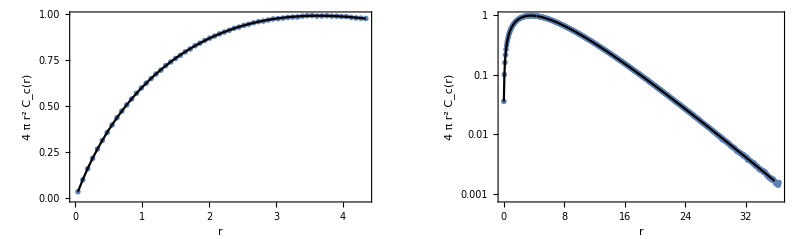

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->{Black}],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True,PlotStyle->{Black}],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->{Black}],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Infinite 3D, isotropic point source, linearly-anisotropic scattering, Gamma-2 random flight - correlated emission\nCollision-rate density C_c[r], c = "<>ToString[c]<>", b = "<>ToString[b]]
```

### Collision-rate density - Uncorrelated emission - Exact solution (2) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

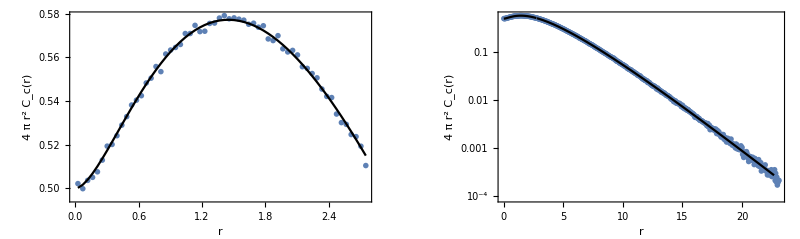

```mathematica
data=SelectFirst[simulationsU,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 Cuexact2[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 Cuexact2[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->{Black}],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True,PlotStyle->{Black}],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->{Black}],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Infinite 3D, isotropic point source, linearly-anisotropic scattering, Gamma-2 random flight - uncorrelated emission\nCollision-rate density C_u[r], c = "<>ToString[c]<>", b = "<>ToString[b]]
```

### Collision-rate density - double and triple scattering

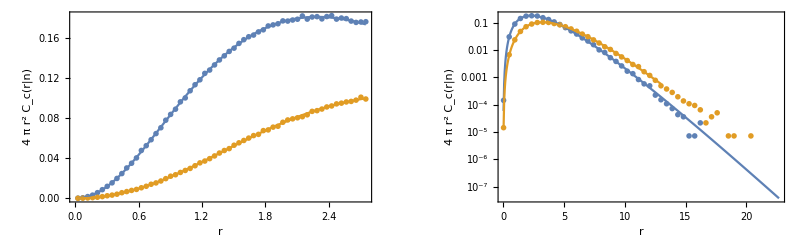

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate2=ppoints[data[[116]],dr,maxr];
MCCollisionRate3=ppoints[data[[117]],dr,maxr];
exact1CR2Shallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 CcDouble[#[[1]],c,b]}]& /@MCCollisionRate2[[1;;60]];
exact1CR2=Quiet[{#[[1]],4 Pi (#[[1]])^2 CcDouble[#[[1]],c,b]}]& /@MCCollisionRate2[[61;;-1;;10]];
exact1CR3Shallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 CcTriple[#[[1]],c,b]}]& /@MCCollisionRate3[[1;;60]];
exact1CR3=Quiet[{#[[1]],4 Pi (#[[1]])^2 CcTriple[#[[1]],c,b]}]& /@MCCollisionRate3[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[{MCCollisionRate2[[1;;60]],MCCollisionRate3[[1;;60]]},PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[{exact1CR2Shallow,exact1CR3Shallow},PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r|n],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[{MCCollisionRate2[[1;;-1;;10]],MCCollisionRate3[[1;;-1;;10]]},PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[{exact1CR2,exact1CR3},PlotRange->All,Joined->True],
ListLogPlot[{exact1CR2Shallow,exact1CR3Shallow},PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r|n],},{r,}},PlotRange->All
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (1)\nInfinite 3D, isotropic point source, linearly-anisotropic scattering, Gamma-2 random flight - correlated emission\n2nd and 3rd Collision-rate density C_c[r|2] and C_c[r|3], c = "<>ToString[c]<>", b = "<>ToString[b]]
```

### Fluence - Exact solution (1) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

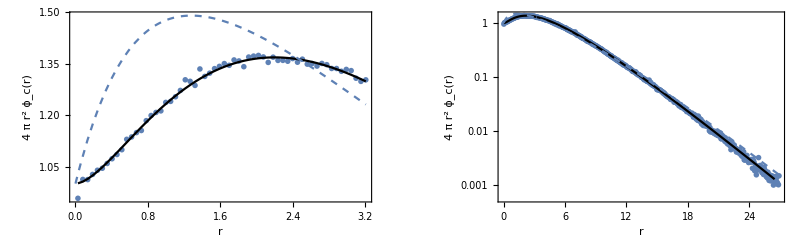

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[6]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕcexact[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕcexact[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->Black],
Plot[4 Pi r^2 fluenceGrosjean[r,c,b],{r,0,MCCollisionRate[[60,1]]},PlotStyle->Dashed],
Frame->True,PlotRange->All,
FrameLabel->{{4 π r^2 Subscript[ϕ, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True,PlotStyle->Black],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->Black],
LogPlot[4 Pi r^2 fluenceGrosjean[r,c,b],{r,0,maxr},PlotStyle->Dashed,PlotRange->All],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[ϕ, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Infinite 3D, isotropic point source, linearly-anisotropic scattering, Gamma-2 random flight - correlated emission\nFluence ϕ_c[r], c = "<>ToString[c]<>", b = "<>ToString[b]]
```

```mathematica
fluenceGrosjean[.1,.8,0.7]
```

8.74066

### Angular distribution - collision rate density and Radiance compared

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

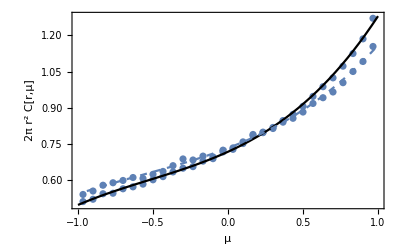

```mathematica
depthi=52;
Clear[u];
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[-1]];
du=data[[2,9]];
maxr=data[[2,5]];
dr=data[[2,7]];
Ci=15+4 numcollorders;
fluxi=17+4 numcollorders+Floor[maxr/dr];
angularFlux =ppointsu[data[[fluxi+depthi]]/2,du,1];
angularC =ppointsu[data[[Ci+depthi]],du,1];
r = dr * depthi-0.5 dr;
af0=Ccexact[r,1,c,b];
af1=Cl[1,r,c,b];
af2=Cl[2,r,c,b];
af3=Cl[3,r,c,b];
ff0=ϕcexactplus[r,1,c,b];
ff1=ϕl[1,r,c,b];
ff2=ϕl[2,r,c,b];
ff3=ϕl[3,r,c,b];
Show[
ListPlot[angularC,PlotRange->All,
Frame->True,
FrameLabel->{{"2π r^2 C[r,μ]",},{μ,"c = " <>ToString[c]<>", b = " <>ToString[b]<>", r = "<>ToString[r]}}],
ListPlot[angularFlux,PlotRange->All],
Plot[ Pi  r^2(af0+ LegendreP[1,u] af1+LegendreP[2,u]af2+LegendreP[3,u]af3),{u,-1,1},PlotRange->All,PlotStyle->Black],
Plot[ 1/2 Pi  r^2(ff0+ LegendreP[1,u] ff1+ LegendreP[2,u] ff2+ LegendreP[3,u] ff3),{u,-1,1},PlotRange->All,PlotStyle->Dashed],PlotRange->All
]
```

## Namespace

```mathematica
End[]
```

inf3DisopointlinanisoscatterGamma2`